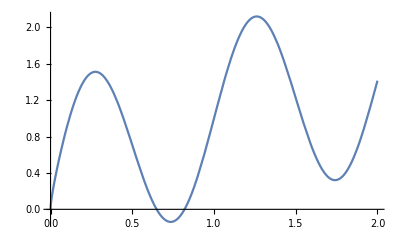

```mathematica
f[x_]:=√x+Sin[2 π x];
a=0;b=2;
Plot[f[x],{x,a,b}]
```

```mathematica
(*So the function is continuous and differentiable in the interval*)
NSolve[f'[c]==(f[b]-f[a])/(b-a)&&c∈Interval[{a,b}],c]
```

{{c→{0.257071}},{c→{0.753319}},{c→{1.24344}},{c→{1.75836}}}